# Числено диференциране

## Параметрите a и b са съответно предпоследната и последната цифра от факултетния номер

1. Да се състави таблицата (z_j, φ(z_j )), където
z_j = −a + j(0.4), j = OverBar[0, 5] ,         φ(z) = √(z^2 + b^2+ 4)
2. Да се намерят първите производни φ_j',  j = OverBar[0, 5]
3. Да се намерят вторите производни φ_j'',  j = OverBar[1, 4]

## Генериране на данни

```mathematica
xt = Table[-6 + j *0.4, {j, 0,5}]
```

{-6.,-5.6,-5.2,-4.8,-4.4,-4.}

```mathematica
f[x_] := √(x^2 + 53)
yt = f[xt]
```

{9.43398,9.18477,8.94651,8.72009,8.50647,8.30662}

```mathematica
h = 0.4
```

0.4

```mathematica
n = Length[xt]
```

6

## Формули с точност O(h^2) - втори порядък

### Първа производна

Попълваме средните точки

```mathematica
yp2 = Table[(yt[[i+1]] - yt[[i-1]])/(2h), {i, 2, n - 1}]
```

{-0.609342,-0.580848,-0.550049,-0.516835}

Допълваме производната в десния край (последната)

```mathematica
AppendTo[yp2, (yt[[n - 2]] - 4yt[[n-1]] + 3yt[[n]])/(2h)]
```

{-0.609342,-0.580848,-0.550049,-0.516835,-0.482386}

Допълваме производната в левия край (първата)

```mathematica
PrependTo[yp2, (-3yt[[1]] +4yt[[2]] - yt[[3]])/(2h)]
```

{-0.636714,-0.609342,-0.580848,-0.550049,-0.516835,-0.482386}

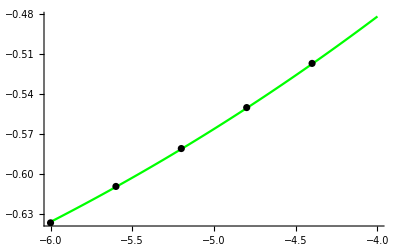

```mathematica
pointsyp2 = Table[{xt[[i]], yp2[[i]]}, {i , 1, n-1}] ;
gryp2 = ListPlot[pointsyp2, PlotStyle->Black];
grfyp = Plot[f'[x], {x, xt[[1]], xt[[n]]}, PlotStyle->Green];
Show[grfyp, gryp2]
```

### Втора производна

Попълваме средните точки

```mathematica
ypp2 = Table[(yt[[i+1]] -2 yt[[i]]+yt[[i-1]])/h^2, {i, 2, n - 1}]
```

{0.0684302,0.0740397,0.0799521,0.0861209}

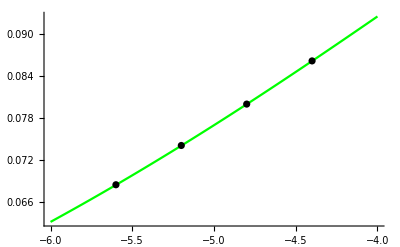

```mathematica
pointsypp2 = Table[{xt[[i + 1]], ypp2[[i]]}, {i , 1, n-2}] ;
grypp2 = ListPlot[pointsypp2, PlotStyle->Black];
grfypp = Plot[f''[x], {x, xt[[1]], xt[[n]]}, PlotStyle->Green];
Show[grfypp, grypp2]
```